```mathematica
ClearAll["Global`*"];
W=Function[s,Exp[-s^2/.16]];
```

The Eulerian formulation picks up extra terms when taking time derivatives via the following relation:
If f(s,t) = F(S0(s,t),t), then f_t=F_t+F_S0(∂S0)/(∂t), and (∂f)/(∂s)=(∂F)/(∂S0)(∂S0)/(∂s)=αγ(∂F)/(∂S0)
Space derivatives translate in a more obvious way: ∂/(∂S0)=∂/(∂s)(∂s)/(∂S0)=αγ∂/(∂s)

```mathematica
(* Before homeostasis *)
Subs={μ->10,ρ->10,ns->-.5,k->1000};
(* note using n = Subscript[E, s](α-1) with Subscript[E, s]=1, so α always appears as α=1+n *)
(* Lagrangian formulation *)
SolPreHomeostasis=NDSolve[{D[s[S0,t],S0]==(1+n[S0, t])γ[S0,t],
D[γ[S0,t],t]==γ[S0,t](W[s[S0,t]]+μ*(n[S0, t]-ns)*1/2*(1+Tanh[10*(ns-n[S0, t])])),
D[n[S0, t], S0]==k*(1+n[S0, t])γ[S0,t]*(s[S0, t]-p[S0, t]),
D[p[S0, t], t]==ρ*(s[S0, t]-p[S0, t]),
s[0,t]==0,s[1,t]==1,γ[S0,0]==1,s[S0,0]==S0, p[S0, 0]==S0, n[S0, 0]==0}/.Subs,{s,γ, n, p},{S0,0,1},{t,0,10}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable S0. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 19.0519 at t = 10. in the direction of independent variable S0 is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
(* Eulerian formulation *)
SolPreHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/((1+n[s, t])γ[s,t]),
D[γ[s,t],t]==γ[s,t](W[s]+μ*(n[s, t]-ns)*1/2*(1+Tanh[10*(ns-n[s, t])]))+(1+n[s,t])*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[n[s, t], s]==k*(s-p[s, t]),
D[p[s, t], t]==ρ*(s-p[s, t])+(1+n[s,t])*γ[s,t]*D[p[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[1,t]==1,γ[s,0]==1,S0[s,0]==s, p[s, 0]==s, n[s, 0]==0}/.Subs,{S0,γ, n, p},{s,0,1},{t,0,10}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
ps=Function[s,p[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
psp=Function[s,Evaluate[ D[p[s, t]/.SolPreHomeostasisEulerian/.t-> 1,s]]];
ns=Function[s,n[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gs=(Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> 1)/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gammas=Function[s, Evaluate[γ[s, t]/.t-> 1/.SolPreHomeostasisEulerian]];
```

```mathematica
gs[0]
```

(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])/(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])[0,1]

(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])/(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])

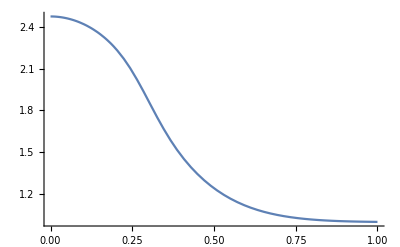

```mathematica
Plot[gammas[s], {s, 0, 1}]
```

```mathematica
(* Solution during homeostasis in Eulerian framework *)SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/((1+ns[s])γ[s,t]),
D[γ[s,t],t]==γ[s,t]gs[s]+D[γ[s,t], s]*(ρ (ps[s]-s))/psp[s],
S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0,10}][[1]];
```

CoefficientArrays::poly: S0$334336 is not a polynomial.

NDSolve::femper: PDE parsing error of S0$334336 - 1/γ (1 + TagBox[InterpolatingFunction[{{0.`, 1.`}, {0.`, 10.`}}, « 3 », {Automatic, Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][s, 1])γ$334337 - γ « 1 »/« 1 » - 10 γ$334338 (-s + TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][s, 1])/TagBox[InterpolatingFunction[{{0.`, 1.`}, {0.`, 10.`}}, « 3 », « 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][s, 1]. Inconsistent equation dimensions.

```mathematica
SolHomeostasisEulerian
```

{S0^(1,0)[s,t]==1/(γ[s,t] (1+InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])),γ^(0,1)[s,t]==(γ[s,t] InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])/(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1])+(10 (-s+InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1]) γ^(1,0)[s,t])/(InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1]),S0[0,t]==0,γ[s,0]==InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,1]}

```mathematica
Subs={μ->2,η->1,ns->-.5,k->100};
(* note using n = Subscript[E, s](α-1) with Subscript[E, s]=1, so α always appears as α=1+n *)
(* Lagrangian formulation *)
Sol1=NDSolve[{D[s[S0,t],S0]==(1+ns)γ[S0,t],
D[γ[S0,t],t]==γ[S0,t](W[s[S0,t]]),
s[0,t]==0,s[1,t]==1,γ[S0,0]==1,s[S0,0]==S0}/.Subs,{s,γ},{S0,0,1},{t,0,10}][[1]];

(* Eulerian formulation *)
Sol2=NDSolve[{D[S0[s,t],s]==1/((1+ns)γ[s,t]),
D[γ[s,t],t]==γ[s,t]*W[s]+(1+ns)γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[0,t]==0,γ[s,0]==1/(1+ns),S0[s,0]==s}/.Subs,{S0,γ},{s,0,1},{t,0,10}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable S0. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at t == 0.; unable to continue.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

Looking at the growth profiles from each solution - note the difference in independent variable means we don’t expect them to align!

```mathematica
Lmu= Function[t,S0[s,t]/.Sol2/.s-> 1];
L=Function[t, Integrate[γ[s,t]/.Sol2,{s, 0, 1}]];
```

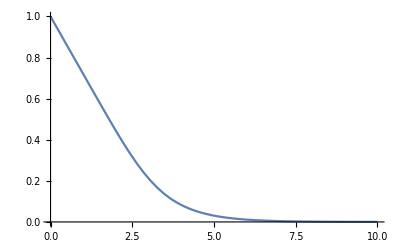

```mathematica
Plot[Lmu[t], {t, 0, 10},PlotRange-> Full]
```

```mathematica
s[Lmu[t],t]/.t-> 5
```

s[0.0306673,5]

```mathematica
Sol1=NDSolve[{D[s[S0,t],S0]==(1+ns)γ[S0,t],
D[γ[S0,t],t]==γ[S0,t](W[s[S0,t]]),
s[0,t]==0,(s[Lmu[2.5],t]==1),γ[S0,0]==1,s[S0,0]==S0}/.Subs,{s,γ},{S0,0,Lmu[2.5]},{t,0,10}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable S0. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndsz: At t == 0.00020001, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Sol1
```

{s→InterpolatingFunction[{{0., 0.316596}, {0., 0.00020001}}, <>],γ→InterpolatingFunction[{{0., 0.316596}, {0., 0.00020001}}, <>]}

```mathematica
Manipulate[ParametricPlot[{s[0(D[γ[s,t],t]/γ[s,t])/.Sol2/.t-> T,{s, 0, 1}],{T, 0, 5}]
```

```mathematica
Manipulate[Plot[(γ[s,t]/.Sol2),{s, 0, 1}],{t, 0.0, 5}]
```

```mathematica
Plot[S0/.Sol2,{s, 0, 1}]
```

-Graphics-

```mathematica
Integrate[1/((1+ns)*γ[s,t])/.Sol2,{s, 0, 1}]
```

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
x
```

To check that both solutions agree, let’s plot the stress n at the end time t=10.
To do this, we first have to invert one of the maps. 
We’ll plot as function of s, so we need to invert the map s(S0,10) in the first solution

```mathematica
ss=Range[0,1,.01];
SS0={};
AppendTo[SS0,0];
For[i=2,i≤Length[ss]-1,i++,
AppendTo[SS0,S0/.NSolve[ss[[i]]==s[S0,t]/.Sol1/.t->10,S0][[1]]];
];
AppendTo[SS0,1];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

First we check the inverted map agrees with the function S0(s,10) from the second solution

```mathematica
Manipulate[Plot[1/2(1+Tanh[σ*(x - 0.1)]),{x, -1, 1}], {σ, 0, 50}]
```

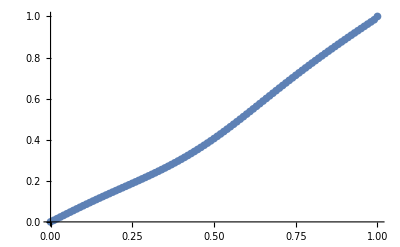

```mathematica
Show[Plot[S0[s,10]/.Sol2,{s,0,1}],ListPlot[Table[{ss[[i]],SS0[[i]]},{i,1,Length[ss]}]]]
```

Now we compare the stress profiles as a function of s

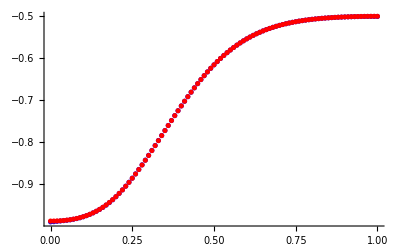

```mathematica
Show[ListPlot[Table[{ss[[i]],n[SS0[[i]],10]/.Sol1},{i,1,Length[ss]}],PlotStyle->Blue],
ListPlot[Table[{ss[[i]],n[ss[[i]],10]/.Sol2},{i,1,Length[ss]}],PlotStyle->Red]]
```